```mathematica
EdgesToColors[edges1_,edges2_]:=Block[{
intersection },
intersection=Intersection[edges1,edges2];
Join[
Map[#->Directive[Yellow,Thick]&,intersection],
Map[#->Directive[Red,Thick]&,SetDifference[edges1,edges2]],
Map[#->Directive[Blue,Thick]&,SetDifference[edges2,edges1]]
]
]
```

```mathematica
Clear[ShowForNodes2];ShowForNodes2[nodes_]:=Flatten[Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]]
},
Labeled[
CompleteGraph[nodes,
EdgeStyle->EdgesToColors[e1,e2],
VertexLabels->"Name",
VertexCoordinates->CoordinatesForNodes[nodes]
],
Multicolumn[{
Map[SetsToLabel,{part1,part2}],
Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2]]]], SymbolLevel[#]==4&& HasTrianglePattern[SymbolToSets[#]]&]
}]
]
]
,
{part1,Take[QuadrilateralsWithPattern[nodes,1],4]},
{part2,Take[QuadrilateralsWithPattern[nodes,5],4]}
],1]
```

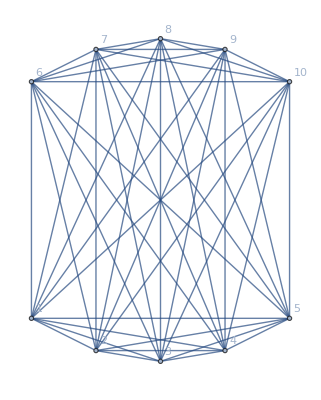
{-Graphics-{137♁2610♁48♁59,1610♁259♁37♁48} | {v137x259x48x6a},-Graphics-{137♁2610♁48♁59,17♁259♁3610♁48} | {v137x259x48x6a},-Graphics-{137♁2610♁48♁59,1610♁259♁38♁47} | {v137x259x48x6a},-Graphics-{137♁2610♁48♁59,18♁259♁3610♁47} | {v137x259x48x6a},-Graphics-{138♁2610♁47♁59,1610♁259♁37♁48} | {v138x259x47x6a},-Graphics-{138♁2610♁47♁59,17♁259♁3610♁48} | {v138x259x47x6a},-Graphics-{138♁2610♁47♁59,1610♁259♁38♁47} | {v138x259x47x6a},-Graphics-{138♁2610♁47♁59,18♁259♁3610♁47} | {v138x259x47x6a},-Graphics-{138♁27♁4610♁59,1610♁259♁37♁48} | {v138x259x46ax7},-Graphics-{138♁27♁4610♁59,17♁259♁3610♁48} | {v138x259x46ax7},-Graphics-{138♁27♁4610♁59,1610♁259♁38♁47} | {v138x259x47x6a,v138x259x46ax7},-Graphics-{138♁27♁4610♁59,18♁259♁3610♁47} | {v138x259x47x6a,v138x259x46ax7},-Graphics-{137♁28♁4610♁59,1610♁259♁37♁48} | {v137x259x48x6a,v137x259x46ax8},-Graphics-{137♁28♁4610♁59,17♁259♁3610♁48} | {v137x259x48x6a,v137x259x46ax8},-Graphics-{137♁28♁4610♁59,1610♁259♁38♁47} | {v137x259x46ax8},-Graphics-{137♁28♁4610♁59,18♁259♁3610♁47} | {v137x259x46ax8}}

```mathematica
ShowForNodes2[10]
```

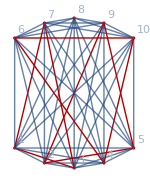

```mathematica
GraphFromSymbol[v137x259x46ax8]
```